```mathematica
(* This Notebook defines modules to find ϕ[n], ϵ[n], η[n], and ns[n]. It does not use the slow roll approx and instead integrates the Klein Gordon equation twice to find ϕ[n]. The first integration uses initial conditions at N=60 from the slow roll approximation. To find the initial conditions for the second integration, we use the solution from the first integration (ϕsol1) to find the value of N where ϵ[n] is 1. Then we set the value of ϕsol1 at that value of N to be the value of ϕ[0] for the initial condition for the second integration. *)
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
```

```mathematica
(* Define an inflationary potential *)
(*v[x_] := x^4*(1-Log[x])*)
v[x_] := x^4
vp[x_]=v'[x]
ni = 60 (* initial value of n for integration *)
nf = -2 (* final value of n for integration *)
(* Define a module to find ϕi (previously ϕ60) *)
```

4 x^3

60

-2

```mathematica
(* Define a module to find ϕ[ni] in the slow roll approx *)
(* This is used to find the initial conditions for the first integration *)
findϕi[v_,vp_,ni_] := Module[{ϕ0},
ϕ0 = x /. Last[NSolve[vp[x]==√2*v[x],x]];
(*Print["ϕ0 = ",ϕ0];*)
f[t_] = Integrate[v[x]/vp[x],{x,ϕ0,t}];
ϕi = t/.Last[NSolve[ni==f[t],t]];
Return[ϕi]]
```

```mathematica
ϕi = findϕi[v,vp,ni]
Print["At N=",ni,", ϕi = ",ϕi]
```

22.0907

At N=60, ϕi = 22.0907

```mathematica
(* Define a module to find ϕ[n] using a single integration *)
findϕ[v_,vp_,ϕi_,ni_,nf_] := Module[{h,hsq,ϕpi},
(* Input: v[n], vp[n], ϕi, ni, nf *)
(* Output: ϕsol (a rule) *)
(* Define H as a function of number of efolds *)
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
(* find ϕpi = ϕ'[ni] for the second initial condition *)
ϕpi = vp[ϕi]/v[ϕi] ;
(* Solve the Klein-Gordon equation for ϕ[n] *)
(* Note that this form of the differential equation only holds provided: 6-(ϕ'[n])^2≠0. *)ϕsol = NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[ni]==ϕi,ϕ'[ni]==ϕpi},ϕ,{n,ni,nf},InterpolationOrder->All];
Return[Last[ϕsol]]]
```

```mathematica
(* Define a module to find ϵ[n], the equation of state *)
findϵ[v_,ϕsol_] := Module[{hsq,ϕp,ϵ},
(* Input: v[n], ϕsol *)
ϕp[n_] = D[ϕ[n],n]/.ϕsol;
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕp[n]^2);
ϵ[n_] := 3*ϕp[n]^2/(ϕp[n]+2*v[ϕ[n]]/hsq[n]);
Return[ϵ[n]]]
```

{ϕ→InterpolatingFunction[{{-2., 60.}}, <>]}

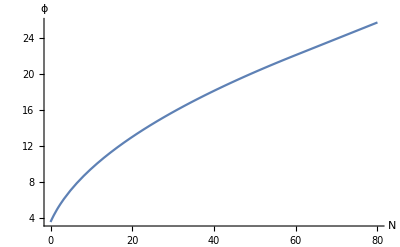

```mathematica
ϕsol = findϕ[v,vp,ϕi,ni,nf]
Plot[Evaluate[ϕ[n]/.ϕsol],{n,80,0},AxesLabel->{N,ϕ}]
```

```mathematica
(* Define a module to find ϕ[n] by integrating twice *)
(* There's something wrong with this module because the ϕ it's returning should be positive and an order of magnitude smaller. I started debugging with the sanity check confirming that the ϕ it returns produces an ϵ that is 1 at n=0. But ϵ[0] does not return a number. I also noticed that if I change the bounds on the NDSolve integration (i.e. change nf to -3, -2, -1, etc.), the nature of the solution changes drastically. I'm not sure what to make of that. *)
findϕ2[v_,vp_,ni_,nf_] := Module[{ϕi,ϕsol1,ϵ1,ϕi1,n1,ϕsol2},
(* Input: v[n], vp[n], ϕi, ni, nf *)
(* Output: ϕsol2 (a rule) *)
ϕi = findϕi[v,vp,ni];
ϕsol1 = findϕ[v,vp,ϕi,ni,nf];
Print["ϕsol1 = ",ϕsol1];
ϵ1[n_]=Last[findϵ[v,ϕsol1]];
Print["ϵ1[n] = ",ϵ1[n]];
n1 = n/.First[NSolve[ϵ1[n]==1,n]]; (* Finds where ϵ is 1. This is where n should be 0 but isn't due to the approximation. Now we'll use the value of ϕ where ϵ is 1 as the new initial condition at n=0. *)
Print["At n1 = ",n1,", ϵ1 = ",Evaluate[ϵ1[n1]]];
ϕi1 = ϕ[n1]/.ϕsol1;
Print["ϕi1 = ",ϕi1];
ϕsol2 = findϕ[v,vp,ϕi1,0,ni];
Return[ϕsol2]]
```

ϕsol1 = {ϕ→InterpolatingFunction[{{-2., 60.}}, <>]}

ϵ1[n] = (1/(InterpolatingFunction[{{-2., 60.}}, <>][n]+2 (3-1/2 (InterpolatingFunction[{{-2., 60.}}, <>][n])^2)))

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

At n1 = -2.49413, ϵ1 = (1/(InterpolatingFunction[{{-2., 60.}}, <>][n]+2 (3-1/2 (InterpolatingFunction[{{-2., 60.}}, <>][n])^2)))

InterpolatingFunction::dmval: Input value {-2.49413} lies outside the range of data in the interpolating function. Extrapolation will be used.

ϕi1 = -0.558341

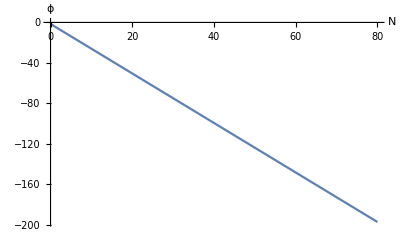

-2.93347

```mathematica
ϕsol = findϕ2[v,vp,ni,nf];
Plot[Evaluate[ϕ[n]/.ϕsol],{n,80,0},AxesLabel->{N,ϕ}]
ϵ[n_]=findϵ[v,ϕsol];
ϵ[0] (* This should be 1, but won't return a number *)
```